62

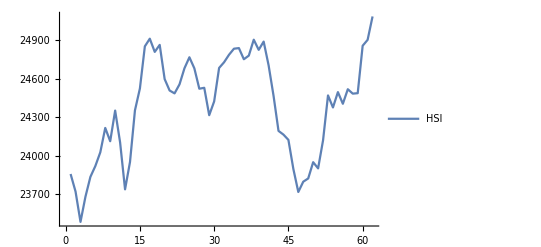

plot.png

```mathematica
stockPrices = FinancialData["^HSI",{DateObject[{2015,1,1}],DateObject[{2015,4,1}]}][[All, 2]];
allRealPrices = stockPrices[[2;;-1]];
allBeforeRealPrices = stockPrices[[1;;-2]];
priceChanges = allRealPrices / allBeforeRealPrices;
Length[stockPrices]
plot = ListLinePlot[{stockPrices},PlotLegends->{"HSI"}]
Export["plot.png", plot]
```

```mathematica
sampleSize = 20;
windowSize =1;
methods = {"NearestNeighbors", "NeuralNetwork", "RandomForest", "LinearRegression"}
predictedPrices = Table[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->priceChanges[[j+windowSize]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Predict[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
If [i == sampleSize, Print[PredictorInformation[#]] & /@ predictors];
#[Keys[testPatterns]] * allBeforeRealPrices[[i]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

{NearestNeighbors,NeuralNetwork,RandomForest,LinearRegression}

Predictor information
Method | K-nearest neighbors
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of neighbors | 5
Distance function | EuclideanDistance

Predictor information
Method | Neural network
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 1
Hidden nodes | ,,1
Hidden layer activation functions | ,,Tanh

Predictor information
Method | Random forest
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of trees | 20

Predictor information
Method | Linear regression
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0.
L2 regularization coefficient | 1.

{NearestNeighbors,NeuralNetwork,RandomForest,LinearRegression}

Predictor information
Method | K-nearest neighbors
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of neighbors | 5
Distance function | EuclideanDistance

Predictor information
Method | Neural network
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 1
Hidden nodes | ,,1
Hidden layer activation functions | ,,Tanh

Predictor information
Method | Random forest
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of trees | 20

Predictor information
Method | Linear regression
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0.
L2 regularization coefficient | 1.

{NearestNeighbors,NeuralNetwork,RandomForest,LinearRegression,Naive}

```mathematica
measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
ListLinePlot[{realPrices, predictedPrices},PlotLegends->{"Real prices", "Predicted Prices"}];
mae = Total[Abs[ predictedPrices-realPrices]] / Length[realPrices];
mape = Total[Abs[ predictedPrices/realPrices-1]] / Length[realPrices]*100;

movementAccuracy = Total[(Sign[predictedPrices-beforeRealPrices] * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];


money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] ≥realPrices[[t-1]], 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{mae, mape, money, N[movementAccuracy]}]
]


table = TableForm[measures,TableHeadings->{methods, {"MAE", "MAPE", "Investment profit", "Movement accuracy"}}]
Export["tidilua.tex", table]
```

| MAE | MAPE | Investment profit | Movement accuracy
NearestNeighbors | 124.662 | 0.508978 | 1.01557 | 0.5
NeuralNetwork | 134.085 | 0.548029 | 1.02543 | 0.5
RandomForest | 146.243 | 0.597261 | 1.02026 | 0.5
LinearRegression | 121.126 | 0.49537 | 0.994371 | 0.452381
Naive | 114.938 | 0.469802 | 1.02349 | 0.5

tidilua.tex

```mathematica
({1,2}+1)/2
```

{1,3/2}

```mathematica
sampleSize = 20;
windowSize =1;
methods = {"NaiveBayes", "LogisticRegression", "NearestNeighbors", "NeuralNetwork", "SupportVectorMachine","RandomForest"};
predictedPrices = Table[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->Sign[priceChanges[[j+windowSize]]-priceChanges[[j+windowSize-1]]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];

predictors = Classify[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
If [i == sampleSize, Print[ClassifierInformation[#]] & /@ predictors];
#[Keys[testPatterns]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

Classifier information
Method | Naive bayes classifier
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1

Classifier information
Method | Logistic regression
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0
L2 regularization coefficient | 1.

Classifier information
Method | K-nearest neighbors
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of neighbors | 5
Distance function | EuclideanDistance

Classifier information
Method | Neural network
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 1
Hidden nodes | ,,2
Hidden layer activation functions | ,,Tanh

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Kernel type | Radial basis function
Soft margin parameter | 1

Classifier information
Method | Random forest
Number of classes | 2
Number of features | 1
Number of training examples | 18
Number of extracted features | 1
Number of trees | 20

{NaiveBayes,LogisticRegression,NearestNeighbors,NeuralNetwork,SupportVectorMachine,RandomForest,Naive}

```mathematica
measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
movementAccuracy = Total[(predictedPrices * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];
money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] > 0, 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{N[(money-1)*100,3], N[movementAccuracy,3]*100}]
]


table = TableForm[measures,TableHeadings->{methods, {"Investment profit", "Movement accuracy"}}]
```

| Investment profit | Movement accuracy
NaiveBayes | 0.296675 | 57.1
LogisticRegression | -0.724724 | 50.
NearestNeighbors | 2.46335 | 59.5
NeuralNetwork | 0.512169 | 52.4
SupportVectorMachine | -1.32635 | 42.9
RandomForest | 2.13425 | 59.5
Naive | 2.34912 | 174505.